#### integral I(g)

```mathematica
∫_(-∞)^(+∞) ⅇ^(-x^2+g*x^4)ⅆx
```

ConditionalExpression[(ⅇ^(-1/8/g) BesselK[1/4,-1/(8 g)])/(2 √-g),Re[g]<0]

```mathematica
i[g_]:=∫_(-∞)^(+∞) ⅇ^(-x^2+g*x^4)ⅆx
```

```mathematica
i[-0.5]
```

1.48631

```mathematica
i[0]
```

√π

```mathematica
i[0.5]
```

Integrate::idiv: Integral of ⅇ^-x^2 + 0.5\ x^4 does not converge on {-∞, ∞}.

∫_(-∞)^∞ ⅇ^(-x^2+0.5 x^4)ⅆx

```mathematica
Sg[g_,m_]:=Sum[Gamma[2n+1/2]/(n!)*g^n,{n,0,m}]
```

```mathematica
Gamma[2n+1/2]/(n!)*g^n
```

```mathematica
Sg[-0.5,100]
```

4.68718×10^185

```mathematica
DiscretePlot[Sg[-1/2,n],{n,1,20}]
```

-Graphics-

```mathematica
N[Sg[-1/2,1]]
```

1.10778

```mathematica
N[i[-50]]
```

0.650765

```mathematica
N[Sg[-50,3]]
```

-5.98313×10^6

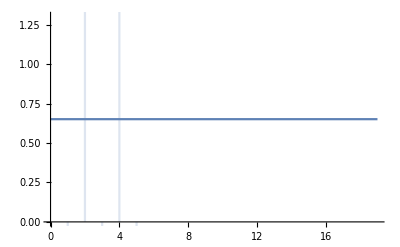

```mathematica
Show[Plot[t=N[i[-50]],{t,0,19}],DiscretePlot[Sg[-50,n],{n,1,5}]]
```

```mathematica
N[i[-167]]
```

0.491459

```mathematica
N[Sg[-167,167]]
```

-1.96113907617791×10^769

```mathematica
N[Sg[-167,1]]
```

-220.227

```mathematica
N[i[-0.00006]]
```

1.77237

```mathematica
N[Sg[-0.00006,1]]
```

1.77237

```mathematica
Table[N[i[-k]],{k,0.040,0.050,0.0020}]
```

{1.72646,1.72445,1.72247,1.7205,1.71856,1.71664}

```mathematica
Table[N[Sg[-k,1]],{k,0.040,0.050,0.0020}]
```

{1.71928,1.71662,1.71396,1.7113,1.70865,1.70599}

```mathematica
Table[N[Sg[-0.04,k]],{k,1,10}]
```

{1.71928,1.72859,1.72551,1.72701,1.72604,1.72682,1.72607,1.72692,1.72583,1.7274}

```mathematica
N[Sg[-0.04,15]]
```

1.69889

```mathematica
Eg[y_,k_]:=Abs[(i[y]-Sg[y,k])]/i[y]*100
```

```mathematica
Do[c=NumberForm[N[Normal[Eg[g,m]]],30];g=-0.040;Print[m,"|"c];Clear[x],{m,1,10}]
```

1| 0.4156473347815865

2| 0.1233401409837222

3| 0.0545257260188408

4| 0.03218388414490994

5| 0.02383052402087985

6| 0.02126107455257463

7| 0.02222010978611362

8| 0.02664187111448938

9| 0.03606433770795371

10| 0.0544207216228325

```mathematica
Do[c=NumberForm[N[Normal[Eg[g,m]]],30];g=-0.040;Print[m,"|"c];Clear[x],{m,10,20}]
```

10| 0.0544207216228325

11| 0.0906021507409536

12| 0.165000661800224

13| 0.3263465909231581

14| 0.6967085817115986

15| 1.596981115335532

16| 3.912174825759533

17| 10.20098642333989

18| 28.2103341096257

19| 82.4749184787883

20| 254.1742772688728

```mathematica
Show[Plot[t=N[i[-0.040]],{t,0,19}],DiscretePlot[Sg[-0.040,n],{n,1,15}],PlotRange->{1.688,1.760}]
```

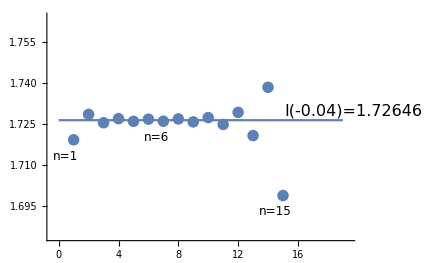

```mathematica
Sn[M_,x_]:=Sum[(-1)^n*n!*x^n,{n,0,M}]
```

```mathematica
Table[Sn[M,0.1],{M,1,10}]
```

{0.9,0.92,0.914,0.9164,0.9152,0.91592,0.915416,0.915819,0.915456,0.915819}

```mathematica
Table[n!*(0.1)^n,{n,1,13}]
```

{0.1,0.02,0.006,0.0024,0.0012,0.00072,0.000504,0.0004032,0.00036288,0.00036288,0.000399168,0.000479002,0.000622702}